# Unfolding

## Definitions and packages (you shall manually execute this section)

Change this line to load the package QMB in https://github.com/deleonja/libs from wherever it is in your machine (make sure you have the up to date version of the package):

```mathematica
Needs["QMB`"]
```

SetDelayed::write: Tag Commutator in Commutator[A_,B_] is Protected.

```mathematica
?Unfold
```

## Bose-Hubbard

## Ising chain

Consider the eigenergies of the odd symmetric subspace of the Ising Hamiltonian with transverse and longitudinal fields

for a set of parameters in which the system is chaotic (h_x=1, h_z=0.48, J=1.12):

```mathematica
SetDirectory[NotebookDirectory[]];(*set the directory to the same of this notebook*)
energies=Catenate@Import["energies_ising_chaotic.csv"];
```

The density of states (DOS) is well approximated by a Gaussian distribution:

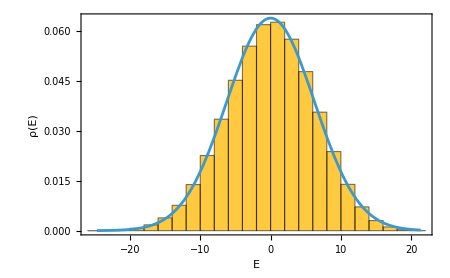

```mathematica
skd=SmoothKernelDistribution[energies];
{μ,σ}={Moment[skd,1],√(Moment[skd,2]-Moment[skd,1]^2)};
Show[
Histogram[energies,Automatic,"PDF",
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"E","ρ(E)"},
ImageSize->450],
Plot[PDF[NormalDistribution[μ,σ],x],{x,Min[energies],Max[energies]}]
]
```

```mathematica
(*Unfold the WHOLE spectrum*)
{unfoldedEnergies,smoothCDF}={#["UnfoldedLevels"],#["SmoothCDF"]}&@Unfold[Sort[energies]];
```

Verify the unfolding worked by checking the mean level spacing is approximately 1:

```mathematica
Mean[Differences[unfoldedEnergies]]
```

1.00003

Compare the staircase function with the smoothed version used to unfold the spectrum:

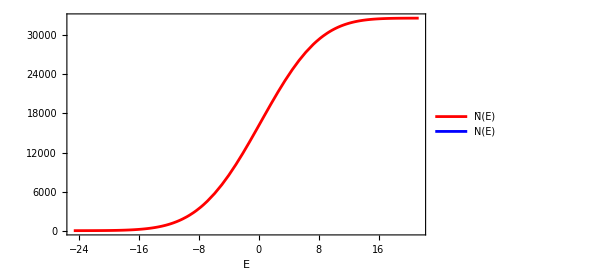

```mathematica
Plot[{smoothCDF[x],Length[energies]*CDF[energies,x]},{x,Min[energies],Max[energies]},
PlotStyle->{Red,Blue},
PlotLegends->Placed[LineLegend[{"N̄(E)","N(E)"},LabelStyle->Directive[FontSize->20]],{Left,Top}],
Frame->True,
FrameStyle->Directive[Black,FontSize->22],
FrameLabel->{"E",""},
ImageSize->450
]
```

After unfolding, the density of states has become almost flat (as should be):

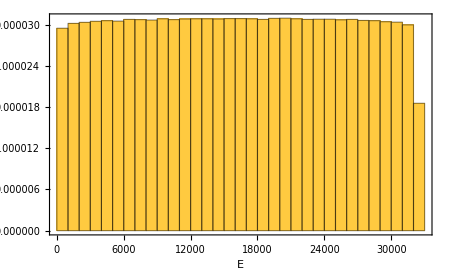

{{0.,1000.,2000.,3000.,4000.,5000.,6000.,7000.,8000.,9000.,10000.,11000.,12000.,13000.,14000.,15000.,16000.,17000.,18000.,19000.,20000.,21000.,22000.,23000.,24000.,25000.,26000.,27000.,28000.,29000.,30000.,31000.,32000.,33000.},{0.0000295037,0.0000302083,0.0000303615,0.0000305147,0.0000306066,0.0000305453,0.0000307904,0.0000307598,0.0000306985,0.0000308824,0.0000307598,0.0000308517,0.0000308824,0.0000308824,0.0000308517,0.000030913,0.000030913,0.0000308824,0.0000307904,0.0000309436,0.0000309743,0.0000308824,0.0000307904,0.0000308211,0.0000308211,0.0000307292,0.0000307904,0.0000306373,0.0000306066,0.0000304534,0.0000303922,0.0000299939,0.0000185662}}

```mathematica
Histogram[unfoldedEnergies,Automatic,"PDF",
Frame->True,
FrameStyle->Directive[Black,FontSize->15],
FrameLabel->{"E",""},
ImageSize->450
]
N[HistogramList[unfoldedEnergies,Automatic,"PDF"]]
```

We compute the level spacing distribution P(s) of the unfolded spectrum only within the bulk (where the ρ(E) of unfolded energies is constant):

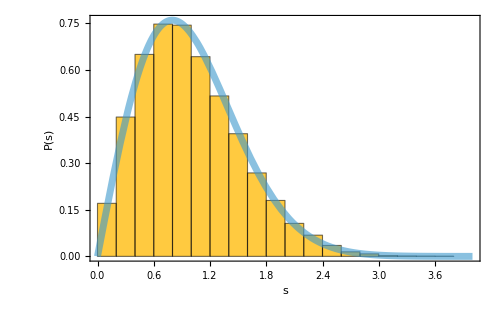

```mathematica
Show[
Histogram[Differences[unfoldedEnergies[[1000;;30000]]],Automatic,"PDF",
PlotRange->{{0,4},All},
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"s","P(s)"},
ImageSize->500
],
(*wigner surmise*)
Plot[PDF[RayleighDistribution[√(2/π)],s],{s,0,4},PlotStyle->Directive[Thickness[0.01],Opacity[0.6]]]
]
```